## 01 Exploratory Data Analysis

## Ejercicios

Import the 2018 Storm Events data and determine on which months have the most tornadoes.

#### Solución

Se importan los datos correspondientes a 2018 Storm Events:

```mathematica
stormEvents2018=Import["/Users/david/Documents/Doctorado en IA/Materias/Semestre 5/Análisis de Datos/1 Exploratory Data Analysis/StormEvents/StormEvents_2018.csv",{"CSV","Dataset"},"HeaderLines"->1]
```

Dataset[<>]

Se seleccionan los eventos correspondientes a tornados :

```mathematica
stormEvents2018Tornado=stormEvents2018[Select[#"Event_Type"=="Tornado"&]]
```

Dataset[<>]

Se agrupan y se cuentan los elementos por la columna de mes  y se grafican para una mejor inspección:

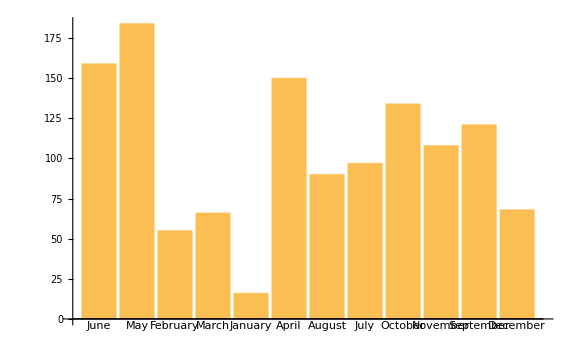

```mathematica
{stormEvents2018Tornado[CountsBy["Month"]],BarChart[stormEvents2018Tornado[CountsBy["Month"]],ChartLabels->Automatic,ImageSize->Large]}
```

Se selecciona el mes con mayor número de eventos :

```mathematica
TakeLargest[stormEvents2018Tornado[CountsBy["Month"]],1]
```

Using the same data set, which is the third most frequent event type?

```mathematica
TakeLargest[stormEvents2018[CountsBy["Event_Type"]],3]
```

Import the file named “hw1.csv” available in the Teams Files of the course (here).

Se importa el archivo hw1 :

```mathematica
hw1=Import["/Users/david/Documents/Doctorado en IA/Materias/Semestre 5/Análisis de Datos/1 Exploratory Data Analysis/hw1.csv","Data"];
Short[hw1,10]
```

{{,region,area,palmitic,palmitoleic,"stearic",oleic,linoleic,linolenic,arachidic,eicosenoic},{1.North-Apulia,1,1,1075,"75","226","7823","672","36","60","29"},{2.North-Apulia,1,1,1088,"73","224","7709","781","31","61","29"},{3.North-Apulia,1,1,911,"54","246","8113","549","31","63","29"},«566»,{570.West-Liguria,3,8,1010,"90","210","7720","970","0","0","2"},{571.West-Liguria,3,8,990,"120","250","7750","870","10","10","2"},{572.West-Liguria,3,8,960,"80","240","7950","740","10","20","2"}}

Identify the data types on each column

Obtengo el tipo de dato de cada elemento en el archivo :

```mathematica
hw1TipoDato=Partition[Map[Head,Flatten[Rest[hw1]]],Length[hw1[[2]]]];
Short[hw1TipoDato,10]
```

{{String,Integer,Integer,Integer,String,String,String,String,String,String,String},{String,Integer,Integer,Integer,String,String,String,String,String,String,String},{String,Integer,Integer,Integer,String,String,String,String,String,String,String},{String,Integer,Integer,Integer,String,String,String,String,String,String,String},{String,Integer,Integer,Integer,String,String,String,String,String,String,String},«563»,{String,Integer,Integer,Integer,String,String,String,String,String,String,String},{String,Integer,Integer,Integer,String,String,String,String,String,String,String},{String,Integer,Integer,Integer,String,String,String,String,String,String,String},{String,Integer,Integer,Integer,String,String,String,String,String,String,String}}

Cuento los tipos de datos que hay en cada columna :

```mathematica
Map[Counts,Transpose[hw1TipoDato]]
```

{<|String→572|>,<|Integer→572|>,<|Integer→572|>,<|Integer→572|>,<|String→572|>,<|String→572|>,<|String→572|>,<|String→572|>,<|String→572|>,<|String→572|>,<|String→572|>}

Plot the values of columns 5 through 11, each column individually, beginning from the second row

Se mapea dos veces la función ToExpression para convertir los datos de tipo string a números:

```mathematica
hw1Column5a11=Partition[Map[ToExpression[ToExpression[#]]&,Flatten[hw1[[2;;,5;;]]]],Length[hw1[[2,5;;]]]];
Short[hw1Column5a11,10]
```

{{75,226,7823,672,36,60,29},{73,224,7709,781,31,61,29},{54,246,8113,549,31,63,29},{57,240,7952,619,50,78,35},{67,259,7771,672,50,80,46},{49,268,7924,678,51,70,44},{66,264,7990,618,49,56,29},{61,235,7728,734,39,64,35},{60,239,7745,709,46,83,33},{55,213,7944,633,26,52,30},{35,219,7978,605,21,65,24},{59,235,7868,661,30,62,44},{70,214,7728,747,50,79,33},{52,243,8018,655,41,79,32},«544»,{90,240,7800,850,0,0,2},{90,300,7650,830,0,10,1},{90,290,7710,800,10,0,2},{120,280,7630,770,10,10,2},{80,240,7820,760,10,0,2},{90,250,7720,810,0,10,3},{90,230,7810,750,0,10,2},{110,210,7720,950,0,0,1},{100,220,7730,870,10,10,2},{110,290,7490,790,10,10,2},{100,270,7740,810,10,10,3},{90,210,7720,970,0,0,2},{120,250,7750,870,10,10,2},{80,240,7950,740,10,20,2}}

Se obtiene la transpuesta para graficar por columnas:

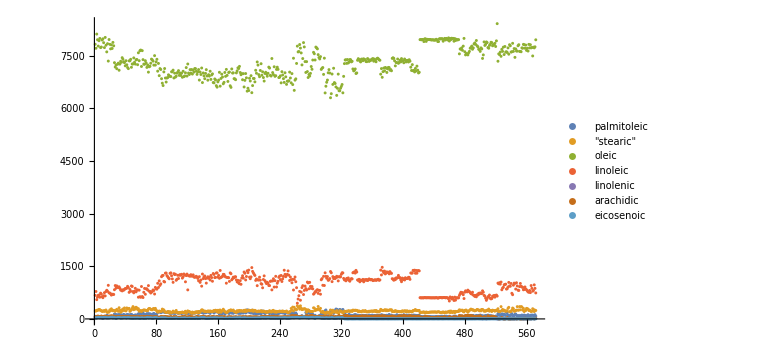

```mathematica
ListPlot[
Transpose[hw1Column5a11],
PlotRange->All,
PlotLegends->hw1[[1,5;;]],
ImageSize->Large]
```

Plot the values of columns 11 and 5 together. The plot should look like this:

Se obtienen las columnas 11 y 5 y se grafican como pares ordenados (x, y) :

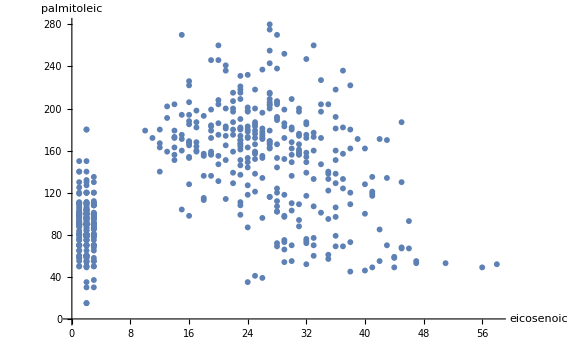

```mathematica
ListPlot[
hw1Column5a11[[All,{-1,1}]],
PlotRange->All,
ImageSize->Large,
AxesLabel->hw1[[1,{11,5}]]]
```